```mathematica
lengthatom=6;
rownumber=4;
ldosdat=Import["wmax3.5_Ny15_Nx15_eta0.12_Ns40_ldostotal.dat"];
sldosdat=Table[Total[Partition[ldosdat[[All,2]],6][[i]]],{i,1,2*lengthatom*rownumber}];
```

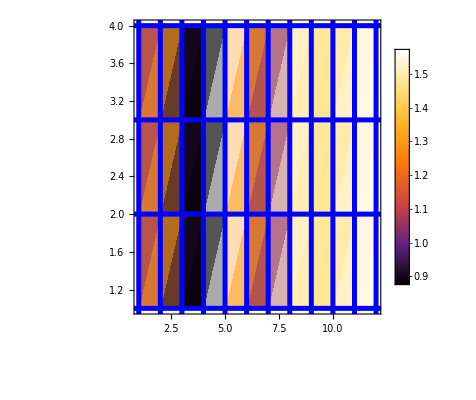

```mathematica
ldosdata=Partition[Partition[sldosdat,lengthatom*rownumber][[1]],lengthatom];
ldosdatb=Partition[Partition[sldosdat,lengthatom*rownumber][[2]],lengthatom];
srldosdata=Table[ldosdata[[All,i]],{i,1,lengthatom}];
srldosdatb=Table[ldosdatb[[All,i]],{i,1,lengthatom}];

ldosplotdat=Table[Flatten[Table[{srldosdata[[n,m]],srldosdatb[[n,m]]},{n,1,lengthatom}]],{m,1,rownumber}];
plot=ListDensityPlot[ldosplotdat,PlotRange->All,
LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]},PlotLegends->Placed[Automatic,{Scaled[{1,0.5}], {0.01, 0.55}}],
Epilog -> {Rotate[Text[Style["Site",25],{-2,2.5}],Pi/2],Text[Style["Site",25],{6.5, 0.3}]},
PlotRangeClipping -> False,ImagePadding->{{70,65},{60,7}},ColorFunction->"SunsetColors",GridLinesStyle->Directive[Blue,Thickness[0.009]],GridLines->{Table[n,{n,1,15}],Table[m,{m,1,6}]}]
Export["ldosplot.eps",plot];
```